# Regge hidden-region audit of the 16 four-loop No-Crown graphs

## Interior and every contraction boundary in T23, T12 and T13 - 23 July 2026

Purpose. This notebook is a self-contained Regge record for the sixteen four-loop massless 2->2 graphs that have mixed-sign derivative factors but no three-loop Crown contraction minor. It defines the three limits, reconstructs the graph polynomials, states the exact graph/channel maps, and records both the interior and complete boundary certificates.

## 1. Final result

quantity | result
graphs | 16
Regge channels | 3
graph/channel interiors | 48
interior hidden-region cases | 0
expanded nonempty contraction strata | 343356
boundary hidden-region strata | 0
unresolved interior or boundary faces | 0
conclusion | No No-Crown HR in the full three-channel Regge audit

The statement is complete for this graph sample: all 48 interiors and all 343356 nonempty contraction strata through E-2 are resolved. No face is left undecided. Together with the independent wide-angle audit of the same graphs, this supports the wide-angle-to-Regge conjecture through four loops for this complete No-Crown sample.

This is evidence for the conjecture, not a general theorem. Regge specialization can delete a kinematic sector and may expose a face that was absent at wide angle. The boundary proof below identifies exactly why that possibility does not occur here.

## 2. Regge kinematics

All external momenta are algebraically incoming and s13=-s12-s23. A Regge channel holds one invariant s fixed and writes its spacelike transfer as t=-delta s with delta>0. The three conventions used by HRF are:

label | small invariant t | large invariant s | delta=-t/s | strict substitution
T23 | s23 | s12 | -s23/s12 | s23→0
T12 | s12 | s23 | -s12/s23 | s12→0
T13 | s13 | s12 | -s13/s12 | s23→-s12

After division by the indicated large invariant, the polynomial has the form F/s=F_Regge,0+delta F_Regge,1. The audit keeps the absolute delta power when a contraction annihilates F_Regge,0; it never silently resets the relative weight of U.

```mathematica
<<"HRF_Example02ReggeKinematics.wl";hrfReggeChannelAssociation[]
```

## 3. Graphs and polynomial definitions

The ordered internal edge list defines x0,x1,... . Setting xi=0 contracts that edge. SymanzikUF constructs U and the second Symanzik polynomial; makeFourPointOnShellF0 then imposes massless four-point kinematics. The displayed lists therefore determine every expression used below.

ID | E | ordered internal edges (x0,x1,...) | external attachments
85774 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,1},{p2,2},{p3,3},{p4,9}}
85775 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,1},{p2,2},{p3,9},{p4,3}}
85776 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,1},{p2,9},{p3,2},{p4,3}}
85777 | 12 | {{0,{1,4}},{0,{1,5}},{0,{2,4}},{0,{2,6}},{0,{3,4}},{0,{3,7}},{0,{5,8}},{0,{5,9}},{0,{6,8}},{0,{6,9}},{0,{7,8}},{0,{7,9}}} | {{p1,9},{p2,1},{p3,2},{p4,3}}
105230 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,1},{p2,2},{p3,3},{p4,4}}
105231 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,1},{p2,2},{p3,4},{p4,3}}
105232 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,1},{p2,4},{p3,2},{p4,3}}
105233 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,1},{p3,3},{p4,4}}
105234 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,1},{p3,4},{p4,3}}
105235 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,4},{p2,1},{p3,2},{p4,3}}
105236 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,3},{p3,1},{p4,4}}
105237 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,4},{p3,1},{p4,3}}
105238 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,4},{p2,2},{p3,1},{p4,3}}
105239 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,3},{p3,4},{p4,1}}
105240 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,2},{p2,4},{p3,3},{p4,1}}
105241 | 13 | {{0,{1,5}},{0,{1,6}},{0,{2,5}},{0,{2,7}},{0,{3,5}},{0,{3,8}},{0,{4,6}},{0,{4,9}},{0,{6,10}},{0,{7,9}},{0,{7,10}},{0,{8,9}},{0,{8,10}}} | {{p1,4},{p2,2},{p3,3},{p4,1}}

```mathematica
SetDirectory[NotebookDirectory[]];$HRFRunWideAngle16NoCrownAuditOnLoad=False;<<"HRF_WideAngle16NoCrownAudit.wl";<<"HRF_WideAngle16ReggeBoundaryAudit.wl";rawRecords=hrfWA16ParseDiagramRecords[hrfWA16InputFile[]];records=hrfWA16BuildData/@rawRecords;
```

## 4. Mapping the three channels

There is no universal T23<->T12<->T13 map within a fixed labelled graph. For example, 85774/T23 maps to 85774/T13, but 85774/T12 belongs to another class; the three channels of 105230 are all distinct parent classes. Exact graph relabellings and explicit Schwinger-variable permutations nevertheless reduce the 48 cases first to twelve exact triples and then to six audit-invariant classes.

The certified object is {F_Regge,0, delta layers, U}. F_Regge,0 agrees exactly up to one overall sign under the recorded permutation, while the delta layers and U have identical exponent supports. This is precisely the information used by the pinch and hierarchy audit.

Each row below is one equivalence class. The directly audited representative is written as diagram/channel. The member column lists every one of the 48 diagram/channel cases transported to that representative; the final column is only the number of those cases, not a diagram symmetry factor or an amplitude multiplicity.

audit class | directly audited representative | propagators E | represented diagram/channel cases | number of represented cases
1 | <|ID→85774,Channel→T23|> | 12 | 85774/T13, 85774/T23, 85775/T12, 85775/T13
85775/T23, 85777/T12 | 6
2 | <|ID→85774,Channel→T12|> | 12 | 85774/T12, 85776/T12, 85776/T13, 85776/T23
85777/T13, 85777/T23 | 6
3 | <|ID→105230,Channel→T23|> | 13 | 105230/T23, 105231/T13, 105233/T13, 105234/T23
105235/T12, 105239/T12 | 6
4 | <|ID→105230,Channel→T12|> | 13 | 105230/T12, 105232/T13, 105232/T23, 105234/T12
105235/T13, 105235/T23, 105236/T13, 105236/T23
105237/T12, 105239/T13, 105239/T23, 105241/T12 | 12
5 | <|ID→105230,Channel→T13|> | 13 | 105230/T13, 105231/T12, 105231/T23, 105233/T12
105233/T23, 105234/T13, 105237/T13, 105238/T12
105238/T23, 105240/T12, 105240/T23, 105241/T13 | 12
6 | <|ID→105232,Channel→T12|> | 13 | 105232/T12, 105236/T12, 105237/T23, 105238/T13
105240/T13, 105241/T23 | 6

### All 48 graph/channel assignments

diagram | channel | E | audit class
85774 | T13 | 12 | 1
85774 | T23 | 12 | 1
85775 | T12 | 12 | 1
85775 | T13 | 12 | 1
85775 | T23 | 12 | 1
85777 | T12 | 12 | 1
85774 | T12 | 12 | 2
85776 | T12 | 12 | 2
85776 | T13 | 12 | 2
85776 | T23 | 12 | 2
85777 | T13 | 12 | 2
85777 | T23 | 12 | 2
105230 | T23 | 13 | 3
105231 | T13 | 13 | 3
105233 | T13 | 13 | 3
105234 | T23 | 13 | 3
105235 | T12 | 13 | 3
105239 | T12 | 13 | 3
105230 | T12 | 13 | 4
105232 | T13 | 13 | 4
105232 | T23 | 13 | 4
105234 | T12 | 13 | 4
105235 | T13 | 13 | 4
105235 | T23 | 13 | 4
105236 | T13 | 13 | 4
105236 | T23 | 13 | 4
105237 | T12 | 13 | 4
105239 | T13 | 13 | 4
105239 | T23 | 13 | 4
105241 | T12 | 13 | 4
105230 | T13 | 13 | 5
105231 | T12 | 13 | 5
105231 | T23 | 13 | 5
105233 | T12 | 13 | 5
105233 | T23 | 13 | 5
105234 | T13 | 13 | 5
105237 | T13 | 13 | 5
105238 | T12 | 13 | 5
105238 | T23 | 13 | 5
105240 | T12 | 13 | 5
105240 | T23 | 13 | 5
105241 | T13 | 13 | 5
105232 | T12 | 13 | 6
105236 | T12 | 13 | 6
105237 | T23 | 13 | 6
105238 | T13 | 13 | 6
105240 | T13 | 13 | 6
105241 | T23 | 13 | 6

```mathematica
<<"results/wa16_regge_interior_v1_permutation_classes.wl"
```

## 5. Interior face/pinch audit and Landau certificates

This is now a separate audit table. Its face counts refer to the directly audited representative only; they are not multiplied by the number of represented diagram/channel cases. For each representative, every exposed face of the strict Regge-leading Newton polytope was enumerated. A face was rejected by a same-sign derivative, by a Farkas separating combination, or, if necessary, by the exact positive pinch equations and oriented hierarchy LP.

audit class | directly audited representative | F_Regge,0 monomials | Newton faces tested | rejected: same-sign derivative | rejected: Farkas separating combination | accepted HR faces | unresolved faces
1 | <|ID→85774,Channel→T23|> | 60 | 68197 | 68065 | 132 | 0 | 0
2 | <|ID→85774,Channel→T12|> | 60 | 68197 | 68065 | 132 | 0 | 0
3 | <|ID→105230,Channel→T23|> | 72 | 186093 | 185761 | 332 | 0 | 0
4 | <|ID→105230,Channel→T12|> | 105 | 335089 | 334957 | 132 | 0 | 0
5 | <|ID→105230,Channel→T13|> | 105 | 335089 | 334957 | 132 | 0 | 0
6 | <|ID→105232,Channel→T12|> | 72 | 186093 | 185761 | 332 | 0 | 0

After multiplication by the class sizes, 11093616 faces are covered: 11084880 are rejected by a same-sign derivative and 8736 by the Farkas separating certificate. No nonlinear solve remains unresolved.

### Farkas theorem in the course formulation and its use here

Course formulation. Given real vectors N_a, exactly one of the following holds: (1) there is a vector eta such that eta.N_a>0 for every a; or (2) there are numbers alpha_a>=0, not all zero, such that sum_a alpha_a N_a=0. Thus a strict separating direction and a nontrivial positive dependence are mutually exclusive.

Connection with the first sheet. The x_e used here are precisely the projective Schwinger (Feynman) parameters. A first-sheet Landau solution has x_e>=0; on an interior stratum all x_e>0, while a boundary stratum has some x_e=0 and is treated after contracting those edges. The physical Regge channel is also written in coordinates kappa_r>0, with all physical signs placed in the polynomial coefficients.

For a proposed cancellation face F_SL, define L_e=x_e dF_SL/dx_e. On an interior stratum x_e>0, so the equations L_e=0 are equivalent to the ordinary Landau stationarity equations dF_SL/dx_e=0.

Write L_e=sum_a M_(a e) m_a(x,kappa) in the common monomial basis and define N_a=(M_(a 1),...,M_(a E)). Every monomial has the form m_a=product_e x_e^(n_(a e)) product_r kappa_r^(p_(a r)); hence first-sheet positivity x_e>0 together with kappa_r>0 implies m_a(x,kappa)>0.

To avoid confusing the course coefficients alpha_a with the conventional Schwinger parameters, call them lambda_a in this application. Set lambda_a=m_a(x,kappa)>0. The Landau equations then become sum_a lambda_a N_a=0. Thus the nonnegative dependence in alternative (2) is induced by Schwinger-parameter positivity: the lambda_a are positive monomials in the Schwinger and physical kinematic coordinates, not an additional set of independent Landau parameters.

course notation | object in the HRF face test
N_a | coefficient row of monomial m_a across all logarithmic derivatives L_i
alpha_a (renamed lambda_a here) | the induced positive monomial value m_a(x,kappa), not an independent Schwinger parameter
eta | the unrestricted derivative-combination coefficients c_i

The audit searches for unrestricted real coefficients c_e such that c.N_a>=0 for every a and c.N_a>0 for at least one a; it also permits the overall opposite sign. This is a weak separating direction. It is already sufficient because, if a first-sheet pinch existed, 0=c.(sum_a lambda_a N_a)=sum_a lambda_a(c.N_a)>0, a contradiction. The strict alternative (1) in the course statement is the special case in which every scalar product is positive.

Equivalently, P=sum_e c_e L_e is a nonzero polynomial whose monomial coefficients all have one sign, so P cannot vanish anywhere in the positive Schwinger domain. Notice that the c_e need not be positive. First-sheet positivity belongs to the x_e and consequently to the induced lambda_a=m_a(x,kappa). The label 'positive-combination certificate' was therefore misleading and has been replaced by 'Farkas separating combination'. A same-sign individual derivative is the simplest instance of the same contradiction.

This is where the physical premise that a hidden region originates at a Landau singularity enters the negative proof. For an interior face all x_i are positive. Cases with some x_i=0 are not discarded by this premise: every such set is treated as a separate contraction stratum in the complete boundary audit of Sections 6 and 7, and positivity is imposed only on the remaining active parameters.

The certificate is sufficient, not an alternative definition of a Landau singularity. Faces for which no such separating combination exists are passed to the explicit positive solution of the Landau equations and then to the hierarchy test.

The three-loop Crown is the positive control: its leading Regge polynomial factorizes into the complementary minor factors and exactly one face survives in each channel, with hierarchy gap one. Thus the method distinguishes the known seed from all sixteen No-Crown interiors.

```mathematica
<<"HRF_WideAngle16ReggeInteriorAudit.wl";hrfWA16ReggeInteriorAudit[recordAssociation[85774],"T23"]
```

## 6. Why almost every boundary was already proved

Let P be the exponent support of the parent strict Regge polynomial. Contracting a set S of Schwinger parameters and retaining a nonzero delta^0 polynomial selects P_S={a in P: a_i=0 for every i in S}. Because all exponents are nonnegative, P_S is the coordinate face minimizing sum_{i in S} a_i. Every exposed face of P_S is therefore already an exposed face of P.

The pinch equations also agree. The restricted F_SL depends only on active variables, so its derivatives with respect to contracted variables vanish identically; a positive solution in the active variables would extend to a positive solution of the parent face equations. Since the parent audit found no positive or unresolved face, every nonzero delta^0 restriction is closed without constructing a second face lattice.

This is the exact mechanism by which the interior calculation can be reused for boundaries. It is stronger and safer than transferring a wide-angle negative verdict directly to Regge kinematics.

## 7. Exceptional boundaries with vanishing delta^0 layer

The only genuinely new possibility is a contraction for which the entire delta^0 coefficient vanishes. The first surviving coefficient is then at delta^1. Its absolute power must be retained: relative to this F layer, U has eta=-1 in the augmented hierarchy. The code implements that general LP even though no such LP is needed for the final negative result.

For every exceptional No-Crown contraction, the delta^1 coefficient is subtraction-free up to one overall sign. Consequently it has no positive cancellation hypersurface and no hidden region. The three exact boundary certificates partition all 343356 strata:

class | representative | full multiplicity | E | codimensions | direct boundaries | inherited q=0 | sign-definite q=1 | trivial | HR | unresolved
1 | <|ID→85774,Channel→T23|> | 6 | 12 | {1,10} | 4082 | 1441 | 416 | 2225 | 0 | 0
2 | <|ID→85774,Channel→T12|> | 6 | 12 | {1,10} | 4082 | 1441 | 416 | 2225 | 0 | 0
3 | <|ID→105230,Channel→T23|> | 6 | 13 | {1,11} | 8177 | 3031 | 1280 | 3866 | 0 | 0
4 | <|ID→105230,Channel→T12|> | 12 | 13 | {1,11} | 8177 | 3579 | 732 | 3866 | 0 | 0
5 | <|ID→105230,Channel→T13|> | 12 | 13 | {1,11} | 8177 | 3579 | 732 | 3866 | 0 | 0
6 | <|ID→105232,Channel→T12|> | 6 | 13 | {1,11} | 8177 | 3031 | 1280 | 3866 | 0 | 0

channel | graphs | boundaries | inherited q=0 | sign-definite q=1 | trivial | HR | unresolved
T23 | 16 | 114452 | 46520 | 12640 | 55292 | 0 | 0
T12 | 16 | 114452 | 46520 | 12640 | 55292 | 0 | 0
T13 | 16 | 114452 | 46520 | 12640 | 55292 | 0 | 0

After expansion to the full graph list, each channel contains exactly 114452 boundaries with the same totals: 46520 inherited coordinate-face certificates, 12640 sign-definite delta^1 certificates and 55292 trivial restricted polynomials.

```mathematica
<<"results/wa16_regge_boundary_v1_summary.wl"
```

## 8. Positive controls and regression

The known HyperCrown boundary x11=0 remains positive in the Regge audit, so the inherited and sign-definite shortcuts do not erase genuine boundary seeds. The regression also directly enumerates one inherited coordinate face and checks one exceptional delta^1 contraction.

test | pass | detail
Coverage.All343356Boundaries | True | All nonempty contraction sets through E-2 in 48 graph/channel cases
Coverage.SixParentClasses | True | The exact channel/graph maps reduce the direct scan to six parents
Channels.EqualCompleteCoverage | True | T23, T12 and T13 have identical expanded certificate totals
Certificates.PartitionAllBoundaries | True | Every boundary has exactly one of the three complete certificates
Conclusion.NoHiddenOrUnresolvedBoundary | True | No No-Crown boundary survives the necessary pinch test
Conclusion.FullReggeNoCrown | True | Interior and every contraction boundary are both closed
ParentFaceClosure.DirectSpotCheck | True | A small inherited coordinate-face certificate agrees with direct enumeration
ExceptionalLayer.AbsoluteEtaOne | True | A vanishing delta^0 contraction is retained at delta^1 and rejected exactly
PositiveControl.HyperCrownBoundary | True | The known boundary seed is not removed by the negative certificates

<|Channel→T12,ZeroVars→{x11},LeadingReggeEta→0,FaceCount→261,PositivePinchFaceCount→57,UnresolvedFaceCount→0,HiddenRegionQ→True|>

```mathematica
<<"HRF_WideAngle16ReggeBoundaryRegressionTests.wl";hrfRunWA16ReggeBoundaryRegressionTests[]
```

## 9. Wide-angle-to-Regge conclusion

For the Crown, both the wide-angle and Regge limits have a hidden region. For every one of the sixteen No-Crown four-loop graphs, neither the wide-angle audit nor any of the three complete Regge audits has an interior or boundary hidden region. Thus no False->True counterexample occurs anywhere in this sample.

The emerging polynomial criterion is a signed-circuit statement. The Crown retains a balanced factorized circuit after one kinematic sector is suppressed. The No-Crown parent faces have exact derivative certificates; their coordinate subfaces inherit those certificates, while the only new first layers created by contraction are subtraction-free. A general proof of the conjecture would need to show that every positive Regge circuit lifts to an admissible wide-angle circuit, which is not true for arbitrary polynomials and remains a graph-theoretic question.

## 10. Graph drawings

The Schwinger labels follow the ordered internal-edge definitions in Section 3; external legs are dashed.

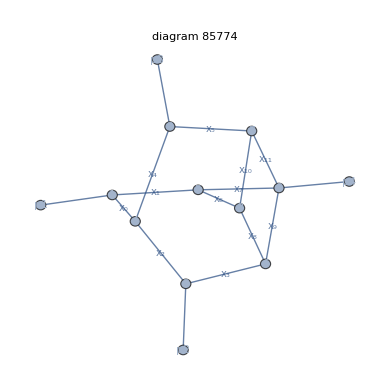
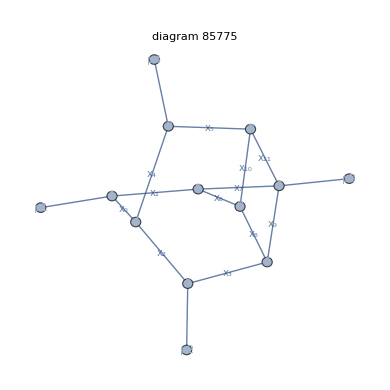
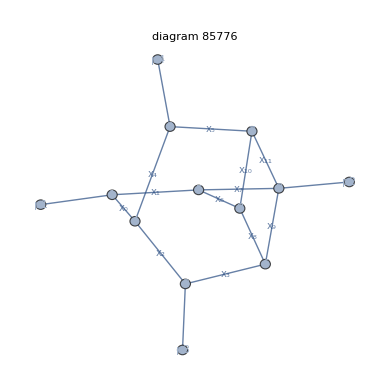
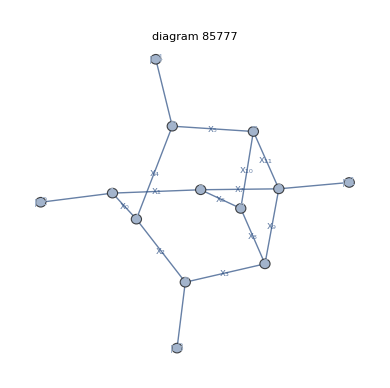
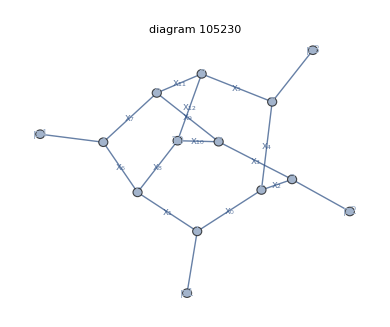
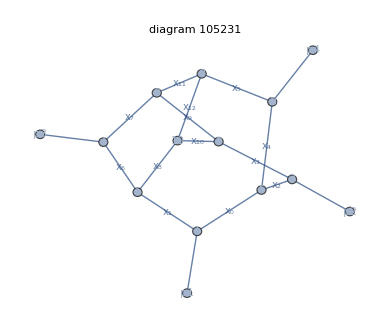
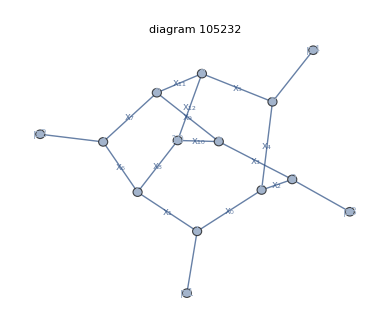
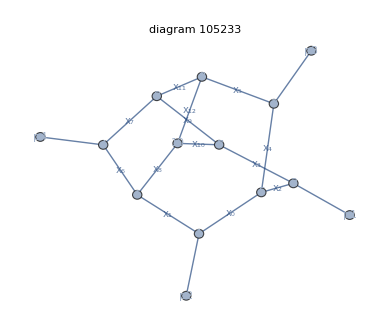

## 11. Polynomial inventory and reproducibility

ID | channel | U terms | strict Regge F terms | suppressed-layer terms
85774 | T23 | 225 | 60 | <|1→60|>
85774 | T12 | 225 | 60 | <|1→60|>
85774 | T13 | 225 | 60 | <|1→60|>
85775 | T23 | 225 | 60 | <|1→60|>
85775 | T12 | 225 | 60 | <|1→60|>
85775 | T13 | 225 | 60 | <|1→60|>
85776 | T23 | 225 | 60 | <|1→60|>
85776 | T12 | 225 | 60 | <|1→60|>
85776 | T13 | 225 | 60 | <|1→60|>
85777 | T23 | 225 | 60 | <|1→60|>
85777 | T12 | 225 | 60 | <|1→60|>
85777 | T13 | 225 | 60 | <|1→60|>
105230 | T23 | 315 | 72 | <|1→105|>
105230 | T12 | 315 | 105 | <|1→72|>
105230 | T13 | 315 | 105 | <|1→105|>
105231 | T23 | 315 | 105 | <|1→105|>
105231 | T12 | 315 | 105 | <|1→105|>
105231 | T13 | 315 | 72 | <|1→105|>
105232 | T23 | 315 | 105 | <|1→72|>
105232 | T12 | 315 | 72 | <|1→105|>
105232 | T13 | 315 | 105 | <|1→72|>
105233 | T23 | 315 | 105 | <|1→105|>
105233 | T12 | 315 | 105 | <|1→105|>
105233 | T13 | 315 | 72 | <|1→105|>
105234 | T23 | 315 | 72 | <|1→105|>
105234 | T12 | 315 | 105 | <|1→72|>
105234 | T13 | 315 | 105 | <|1→105|>
105235 | T23 | 315 | 105 | <|1→72|>
105235 | T12 | 315 | 72 | <|1→105|>
105235 | T13 | 315 | 105 | <|1→72|>
105236 | T23 | 315 | 105 | <|1→72|>
105236 | T12 | 315 | 72 | <|1→105|>
105236 | T13 | 315 | 105 | <|1→72|>
105237 | T23 | 315 | 72 | <|1→105|>
105237 | T12 | 315 | 105 | <|1→72|>
105237 | T13 | 315 | 105 | <|1→105|>
105238 | T23 | 315 | 105 | <|1→105|>
105238 | T12 | 315 | 105 | <|1→105|>
105238 | T13 | 315 | 72 | <|1→105|>
105239 | T23 | 315 | 105 | <|1→72|>
105239 | T12 | 315 | 72 | <|1→105|>
105239 | T13 | 315 | 105 | <|1→72|>
105240 | T23 | 315 | 105 | <|1→105|>
105240 | T12 | 315 | 105 | <|1→105|>
105240 | T13 | 315 | 72 | <|1→105|>
105241 | T23 | 315 | 72 | <|1→105|>
105241 | T12 | 315 | 105 | <|1→72|>
105241 | T13 | 315 | 105 | <|1→105|>

```mathematica
allReggePolynomials=Association[Flatten[Table[rec=records⟦i⟧;Table[{rec["ID"],channel}->Association["Variables"->rec["Vars"],"U"->rec["U"],"FRegge0"->hrfWA16ReggeLeadingPolynomial[rec["F0"],channel],"DeltaLayers"->hrfWA16ReggeLayers[rec["F0"],channel]],{channel,{"T23","T12","T13"}}],{i,Length[records]}]]]
```

```mathematica
RunProcess[{"wolframscript","-file","run_wa16_regge_interior_regression.wl"}]
```

```mathematica
RunProcess[{"wolframscript","-file","run_wa16_regge_boundary_regression.wl"}]
```

Primary files: HRF_WideAngle16ReggeInteriorAudit.wl and HRF_WideAngle16ReggeBoundaryAudit.wl contain the exact certificates; run_wa16_regge_boundary_batch.wl is the checkpointed boundary runner; aggregate_wa16_regge_boundary_audit.wl expands the six representatives to all 48 cases. The compact persisted results are in results/wa16_regge_interior_v1_summary.wl and results/wa16_regge_boundary_v1_summary.wl.

## 12. References

E. Gardi et al., arXiv:2407.13738: original No-Crown evidence and the dissection framework.

E. Gardi et al., arXiv:2607.15126, especially Eqs. (13)-(17): pinch, homogeneous F_SL, ideal presentation and strict hierarchy conditions.